## Collecting data from Bmad

quadNameList =  [“Q5FF”, “Q4FF”, “Q3FF”, “Q2FF”, “Q1FF”, “Q0FF”]
print( [tao.ele_gen_attribs(ele)[“L”] for ele in quadNameList] )
print( [tao.ele_gen_attribs(ele)[“K1”] for ele in quadNameList] )
print( [tao.ele_head(ele)[“s”] for ele in quadNameList] )
print( tao.ele_head(“MFFF”)[“s”] ) 
print( tao.ele_head(“PENT”)[“s”] )
print( tao.ele_twiss(“MFFF”) )
print( tao.ele_twiss(“PENT”) )
print( getMatrix(tao, “MFFF”, “PENT”) )

[0.4609, 0.7142, 0.7142, 0.7142, 0.7142, 0.7142]
[-0.467268800263, -0.34106223812, 0.416509781058, 0.53037956706, -0.987354552247, 0.53037956706]
[979.465596961613, 981.722640961613, 982.632540961613, 989.027839761613, 990.606879761613, 992.184979761613]
979.004696961613
994.772814779842
{‘mode_flip’: False, ‘beta_a’: 11.5533562066009, ‘alpha_a’: -0.640788640830743, ‘gamma_a’: 0.122095264526837, ‘phi_a’: 71.31011993097, ‘eta_a’: 1.82993853116333e-05, ‘etap_a’: 1.18535480249718e-06, ‘beta_b’: 25.2039557159784, ‘alpha_b’: -1.56858472563668, ‘gamma_b’: 0.137298211459199, ‘phi_b’: 56.2536406733655, ‘eta_b’: -2.27197431822392e-17, ‘etap_b’: -4.93465667199839e-20, ‘eta_x’: 1.82993853116333e-05, ‘etap_x’: 1.18535480249718e-06, ‘eta_y’: -2.27197534407484e-17, ‘etap_y’: -4.93522682312884e-20}
{‘mode_flip’: False, ‘beta_a’: 0.500113514905187, ‘alpha_a’: -8.61413026615049e-05, ‘gamma_a’: 1.9995460582782, ‘phi_a’: 73.1003856252222, ‘eta_a’: -4.29100544671707e-07, ‘etap_a’: -7.60864677687215e-06, ‘beta_b’: 0.499955681369933, ‘alpha_b’: 0.000116201966385052, ‘gamma_b’: 2.00017731724298, ‘phi_b’: 60.4082301501082, ‘eta_b’: -6.77061438266227e-18, ‘etap_b’: -1.31862568529448e-17, ‘eta_x’: -4.29100544671707e-07, ‘etap_x’: -7.60864677687215e-06, ‘eta_y’: -6.77059836943936e-18, ‘etap_y’: -1.31862402801866e-17}
[[-1.75418210e-01  2.34608655e+00 -0.00000000e+00  0.00000000e+00
   0.00000000e+00  0.00000000e+00]
 [-3.48031320e-01 -1.04600535e+00 -0.00000000e+00  0.00000000e+00
   0.00000000e+00  0.00000000e+00]
 [ 0.00000000e+00  0.00000000e+00  1.12884820e-01 -3.01170198e+00
   0.00000000e+00 -0.00000000e+00]
 [ 0.00000000e+00  0.00000000e+00  4.72879460e-01 -3.75756449e+00
   0.00000000e+00 -0.00000000e+00]
 [-0.00000000e+00 -0.00000000e+00 -0.00000000e+00  0.00000000e+00
   1.00000000e+00  4.00000000e-08]
 [ 0.00000000e+00  0.00000000e+00  0.00000000e+00  0.00000000e+00
   0.00000000e+00  1.00000000e+00]]

## Sanity check import

Convention:
{{beta, -alpha},{-alpha, gamma}}

```mathematica
{initialBeta,initialAlpha,initialGamma} = {11.5533, -0.64079, 0.122095};
initialTwiss = {{initialBeta, -initialAlpha},{-initialAlpha, initialGamma}}
RMatr = {{-0.1754,2.3461},{-0.34803,-1.0460}}
```

{{11.5533,0.64079},{0.64079,0.122095}}

{{-0.1754,2.3461},{-0.34803,-1.046}}

```mathematica
RMatr . initialTwiss.Transpose[RMatr]
```

{{0.500095,-7.42883×10^-6},{-7.42883×10^-6,1.99952}}

Excellent agreement with expected values of 0.5, 0, and 2

## Recreate final focus matrix

```mathematica
(*{MFFF, [all FF quads], PENT}*)
allSValues = {979.004696961613, 979.465596961613,981.722640961613,982.632540961613,989.027839761613,990.606879761613,992.184979761613, 994.772814779842}
```

{979.005,979.466,981.723,982.633,989.028,990.607,992.185,994.773}

```mathematica
{MFFFToQ5FF, Q5FFToQ4FF,Q4FFToQ3FF,Q3FFToQ2FF,Q2FFToQ1FF,Q1FFToQ0FF,Q0FFToPENT} = Differences[allSValues]
```

{0.4609,2.25704,0.9099,6.3953,1.57904,1.5781,2.58784}

```mathematica
allLValues = {0.4609,0.7142,0.7142,0.7142,0.7142,0.7142}
allK1Values ={-0.467268800263,-0.34106223812,0.416509781058,0.53037956706,-0.987354552247,0.53037956706}
allFocalLengths = 1/(allLValues* allK1Values)
```

{0.4609,0.7142,0.7142,0.7142,0.7142,0.7142}

{-0.467269,-0.341062,0.41651,0.53038,-0.987355,0.53038}

{-4.6433,-4.10532,3.36167,2.63994,-1.4181,2.63994}

```mathematica
drift[l_]:={{1,l},{0,1}}
quadThin[f_]:={{1,0},{-1/f,1}}
quad[l_,K1_]:=(
ϕ = l*√Abs[K1];
If[K1>=0,
{
{Cos[ϕ],1/(√Abs[K1])*Sin[ϕ]},
{-√Abs[K1] Sin[ϕ], Cos[ϕ]}
},
{
{Cosh[ϕ],1/(√Abs[K1])*Sinh[ϕ]},
{√Abs[K1] Sinh[ϕ], Cosh[ϕ]}
}
]
)
```

```mathematica
ClearAll[K1Q5FF,K1Q4FF,K1Q3FF,K1Q2FF,K1Q1FF,K1Q0FF];

{K1Q5FF,K1Q4FF,K1Q3FF,K1Q2FF,K1Q1FF,K1Q0FF}=allK1Values;

RMatrGeneric = 
drift[Q0FFToPENT].
quad[allLValues[[6]],K1Q0FF].
drift[Q1FFToQ0FF-allLValues[[6]]].
quad[allLValues[[5]],K1Q1FF].
drift[Q2FFToQ1FF-allLValues[[5]]].
quad[allLValues[[4]],K1Q2FF].
drift[Q3FFToQ2FF-allLValues[[4]]].
quad[allLValues[[3]],K1Q3FF].
drift[Q4FFToQ3FF-allLValues[[3]]].
quad[allLValues[[2]],K1Q4FF].
drift[Q5FFToQ4FF-allLValues[[2]]].
quad[allLValues[[1]],K1Q5FF].
drift[MFFFToQ5FF-allLValues[[1]]]
```

{{-0.175418,2.34609},{-0.348031,-1.04601}}

Agrees with Bmad output

Exercise caution though! These If[] statements seem to sometimes cause this to give stupid answers with no apparent warning. Advise using this in the simplest way possible, i.e. only call those functions with populated variables, never placeholders/empty variables

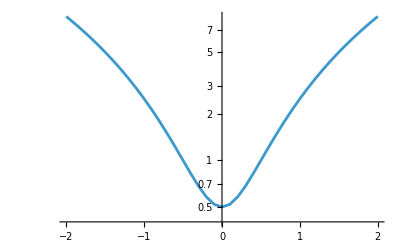

```mathematica
results =Table[
RMatr = drift[Q0FFToPENT+Δs].
quad[allLValues[[6]],K1Q0FF].
drift[Q1FFToQ0FF-allLValues[[6]]].
quad[allLValues[[5]],K1Q1FF].
drift[Q2FFToQ1FF-allLValues[[5]]].
quad[allLValues[[4]],K1Q2FF].
drift[Q3FFToQ2FF-allLValues[[4]]].
quad[allLValues[[3]],K1Q3FF].
drift[Q4FFToQ3FF-allLValues[[3]]].
quad[allLValues[[2]],K1Q4FF].
drift[Q5FFToQ4FF-allLValues[[2]]].
quad[allLValues[[1]],K1Q5FF].
drift[MFFFToQ5FF-allLValues[[1]]];

{Δs,(RMatr.initialTwiss.Transpose[RMatr])[[1,1]]},

{Δs,-2,2,0.1}
];
ListLogPlot[results,Joined->True]
```

## Vary energy

```mathematica
data =Table[
RMatr = drift[Q0FFToPENT+Δs].
quad[allLValues[[6]],K1Q0FF*(10/energy)].
drift[Q1FFToQ0FF-allLValues[[6]]].
quad[allLValues[[5]],K1Q1FF*(10/energy)].
drift[Q2FFToQ1FF-allLValues[[5]]].
quad[allLValues[[4]],K1Q2FF*(10/energy)].
drift[Q3FFToQ2FF-allLValues[[4]]].
quad[allLValues[[3]],K1Q3FF*(10/energy)].
drift[Q4FFToQ3FF-allLValues[[3]]].
quad[allLValues[[2]],K1Q4FF*(10/energy)].
drift[Q5FFToQ4FF-allLValues[[2]]].
quad[allLValues[[1]],K1Q5FF*(10/energy)].
drift[MFFFToQ5FF-allLValues[[1]]];
<| "s"->Δs,"energy"->energy,"betaX"->(RMatr.initialTwiss.Transpose[RMatr])[[1,1]]|>,
{Δs,-2,2,0.01},
{energy,9.0,11.0,0.1}
];
data = Flatten[data,1];

data = GroupBy[data,#energy&];
```

```mathematica
selectedEnergies = {9.0,9.9,10.0,10.1,11.0}
colors = Table[
ColorData["Rainbow"][Rescale[i,{1,Length[selectedEnergies]}]],
{i,Length[selectedEnergies]}
]
```

{9.,9.9,10.,10.1,11.}

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.857359, 0.131106, 0.132128]}

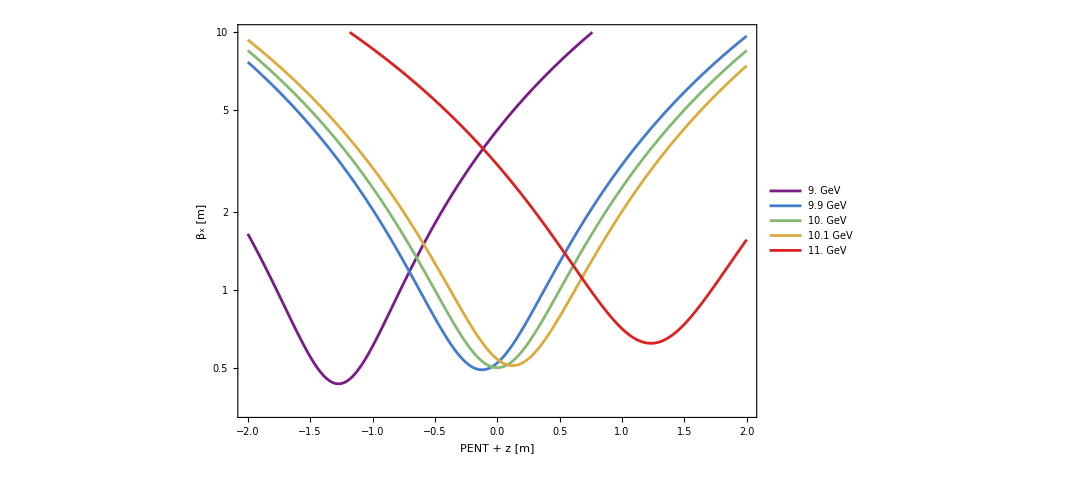

```mathematica
ListLogPlot[
Table[
{#s,#betaX}&/@data[key],
{key,selectedEnergies}
],
Joined->True,
ImageSize->800,
Frame->True,
LabelStyle->20,
PlotRange->{{-2,2},{All,10}},
FrameLabel->{"PENT + z [m]","β_x [m]"},
PlotLegends->((ToString[#]<>" GeV" )&/@selectedEnergies),
PlotStyle->colors
]
```